```mathematica
<<MB.m
```

MB 1.2

by Michal Czakon

improvements by Alexander Smirnov

more info in hep-ph/0511200

last modified 2 Jan 09

```mathematica
<<AMBREv1.2.m
```

by K.Kajda   ver: 1.2 
last modified 9 Apr 2008
last executed on 06.08.2022 at 19:56

```mathematica
<<KinematicsGen.m
```

by K.Kajda ver:1.2

last modification 01 Feb 2007

u::shdw: Symbol u appears in multiple contexts {KinematicsGen`,Global`}; definitions in context KinematicsGen` may shadow or be shadowed by other definitions.

t::shdw: Symbol t appears in multiple contexts {KinematicsGen`,Global`}; definitions in context KinematicsGen` may shadow or be shadowed by other definitions.

Kinematics::shdw: Symbol "Kinematics" appears in multiple contexts {"KinematicsGen`", "Global`"}; definitions in context "KinematicsGen`" may shadow or be shadowed by other definitions.

```mathematica
<<PlanarityTestv1.2.1.m
```

by E. Dubovyk and K. Bielas ver: 1.2.1
created: Aug 2017
last executed: 06.08.2022 at 19:56

```mathematica
inv={p1^2->m^2,p2^2->m^2,p3^2->m^2,p4^2->m^2};
```

```mathematica
choice={s,t};
```

```mathematica
invariants=Kinematics[inv,choice]
```

{p1^2→m^2,p2^2→m^2,p3^2→m^2,p4^2→m^2,p1 p2→1/2 (-2 m^2+s),p1 p3→1/2 (2 m^2-s-t),p2 p3→1/2 (-2 m^2+t),p1 p4→1/2 (-2 m^2+t),p2 p4→1/2 (2 m^2-s-t),p3 p4→1/2 (-2 m^2+s)}

```mathematica
int=PR[k1,0,n1]*PR[k2-p2,0,n2]*PR[k1+k2,m,n3]*PR[k2+p3,0,n4] PR[k2-p1-p2,m,n5];
```

The Diagram

is planar.

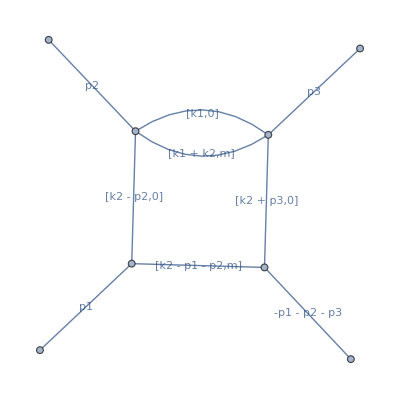

```mathematica
PlanarityTest[{int},{k1,k2},DrawGraph->True];
```

```mathematica
(*
construction of the MB-integral for topology B5l2m2 which is discussed in 
Czakon, J.G.,T.R., PRD71,073009 (2005)    
*)
```

Chapter 4, eq. (4.9)

```mathematica
Fullintegral[
{1},
{PR[k1,0,n1]*PR[k2-p2,0,n2]*PR[k1+k2,m,n3]*PR[k2+p3,0,n4] PR[k2-p1-p2,m,n5]},{k1,k2}];
```

```mathematica
IntPart[1]
```

numerator=1
integral=PR[k1,0,n1] PR[k1+k2,m,n3]
momentum=k1

Fauto::mode: U and F polynomials will be calculated in AUTO mode. In order to use MANUAL mode execute Fauto[0].

```mathematica
SubLoop[integral]
```

Iteration nr1: >>Integrating over k1<<

Computing U & F polynomial in AUTO mode >>Fauto[1]<<

U polynomial...
X[1]+X[2]
F polynomial...
-PR[k2,m] X[1] X[2]+m^2 X[2]^2

Representation after integrating over: k1...

SubLoop1[((-1)^(n1+n3+z1) (m^2)^(2-eps-n1-n3-z1) Gamma[-z1] Gamma[n1+z1] Gamma[-2+eps+n1+n3+z1] Gamma[n3+2 (2-eps-n1-n3-z1)+z1])/(Gamma[n1] Gamma[n3] Gamma[n1+n3+2 (2-eps-n1-n3-z1)+2 z1]),PR[k2,m,z1]]

```mathematica
IntPart[2]
```

numerator=1
integral=PR[k2,m,-z1] PR[k2-p2,0,n2] PR[k2-p1-p2,m,n5] PR[k2+p3,0,n4]
momentum=k2

Fauto::mode: U and F polynomials will be calculated in AUTO mode. In order to use MANUAL mode execute Fauto[0].

```mathematica
repr=SubLoop[integral];
```

Iteration nr2: >>Integrating over k2<<

Computing U & F polynomial in AUTO mode >>Fauto[1]<<

U polynomial...
X[1]+X[2]+X[3]+X[4]
F polynomial...
m^2 FX[X[1]+X[3]]^2-s X[1] X[3]-t X[2] X[4]

Final representation:

((-1)^(n1+n2+n3+n4+n5) (m^2)^(2-eps-n1-n3-z1+z2) (-s)^z3 (-t)^(2-eps-n2-n4-n5+z1-z2-z3) Gamma[n1+z1] Gamma[-2+eps+n1+n3+z1] Gamma[n3+2 (2-eps-n1-n3-z1)+z1] Gamma[-z2] Gamma[2-eps-n2-n5+z1-z2-z3] Gamma[2-eps-n4-n5+z1-z2-z3] Gamma[-z3] Gamma[-2+eps+n2+n4+n5-z1+z2+z3] Gamma[n5+2 z2+z3-z4] Gamma[-z4] Gamma[-2 z2+z4] Gamma[-z1+z3+z4])/(Gamma[n1] Gamma[n2] Gamma[n3] Gamma[n4] Gamma[n5] Gamma[4-2 eps-n2-n4-n5+z1] Gamma[n1+n3+2 (2-eps-n1-n3-z1)+2 z1] Gamma[-2 z2])

```mathematica
BarnesLemma[repr,1]
```

>> Barnes 1st Lemma will be checked for: {z4} <<
   Starting with dim=4 representation...

1. Checking z4

>> Representation after 1st Barnes Lemma:  <<

Could not apply Barnes-Lemma

((-1)^(n1+n2+n3+n4+n5) (m^2)^(2-eps-n1-n3-z1+z2) (-s)^z3 (-t)^(2-eps-n2-n4-n5+z1-z2-z3) Gamma[4-2 eps-2 n1-n3-z1] Gamma[n1+z1] Gamma[-2+eps+n1+n3+z1] Gamma[-z2] Gamma[2-eps-n2-n5+z1-z2-z3] Gamma[2-eps-n4-n5+z1-z2-z3] Gamma[-z3] Gamma[-2+eps+n2+n4+n5-z1+z2+z3] Gamma[n5+2 z2+z3-z4] Gamma[-z4] Gamma[-2 z2+z4] Gamma[-z1+z3+z4])/(Gamma[n1] Gamma[n2] Gamma[4-2 eps-n1-n3] Gamma[n3] Gamma[n4] Gamma[n5] Gamma[4-2 eps-n2-n4-n5+z1] Gamma[-2 z2])

```mathematica
fin=%/.{n1->1,n2->1,n3->1,n4->1,n5->1}
```

-(((m^2)^(-eps-z1+z2) (-s)^z3 (-t)^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+eps-z1+z2+z3] Gamma[1+2 z2+z3-z4] Gamma[-z4] Gamma[-2 z2+z4] Gamma[-z1+z3+z4])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[-2 z2]))

Chapter 4, eq. (4.10)

```mathematica
fin=-((m^2)^(-eps-z1+z2) (-s)^z3 (-t)^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1+eps-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 z3]);
```

Chapter 4, eq. (4.11), remark: actual numbers can differ with Mathematica versions

```mathematica
rules=MBoptimizedRules[fin,eps->0,{},{eps}]
```

MBrules::norules: no rules could be found to regulate this integral

{{eps→5/24},{z1→-1/12,z2→-3/8,z3→-1/24}}

```mathematica
?FindInstance
```

FindInstance[expr,vars] finds an instance of vars that makes the statement expr be True. 
FindInstance[expr,vars,dom] finds an instance over the domain dom. Common choices of dom are Complexes, Reals, Integers, and Booleans. 
FindInstance[expr,vars,dom,n] finds n instances.

```mathematica
backGamma={G1[x__]->Gamma[x],G2[x__]->Gamma[x],G3[x__]->Gamma[x],G4[x__]->Gamma[x],G5[x__]->Gamma[x],G6[x__]->Gamma[x],G7[x__]->Gamma[x],G8[x__]->Gamma[x],G9[x__]->Gamma[x],G10[x__]->Gamma[x],G11[x__]->Gamma[x],G12[x__]->Gamma[x]};
```

```mathematica
aux = G1[1-2 eps-z1] G2[1+z1] G3[eps+z1] G4[-z2] G5[-eps+z1-z2-z3]G6[-z3] G7[1+z3] G8[-z1+z3] G9[1+eps-z1+z2+z3] G10[1-z1+2 z2+2 z3];
```

```mathematica
Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0
```

{1-2 eps-z1>0,1+z1>0,eps+z1>0,-z2>0,-eps+z1-z2-z3>0,-z3>0,1+z3>0,-z1+z3>0,1+eps-z1+z2+z3>0,1-z1+2 z2+2 z3>0}

```mathematica
FindInstance[Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0/.eps->-1/2,{z1,z2,z3}]
```

{}

```mathematica
FindInstance[Cases[aux/.G_[x_]->Gamma[x],Gamma[_]^n_.]/.Gamma[x_]^n_.->x>0/.eps->1/10,{z1,z2,z3}]
```

{{z1→-1/20,z2→-5/16,z3→-1/40}}

```mathematica
subst=%[[1]]
```

{z1→-1/20,z2→-5/16,z3→-1/40}

```mathematica
subst0=Append[subst,eps->0]
```

{z1→-1/20,z2→-5/16,z3→-1/40,eps→0}

```mathematica
aux/.subst/.eps->1/10
```

G1[17/20] G10[3/8] G2[19/20] G3[1/20] G4[5/16] G5[3/16] G6[1/40] G7[39/40] G8[1/40] G9[13/16]

```mathematica
aux/.subst0
```

G1[21/20] G10[3/8] G2[19/20] G3[-1/20] G4[5/16] G5[23/80] G6[1/40] G7[39/40] G8[1/40] G9[57/80]

```mathematica
fin=-((m^2)^(-eps-z1+z2) (-s)^z3 (-t)^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1+eps-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 z3]);
```

Chapter 4, eq. (4.13)

```mathematica
res0=Residue[fin,{z1,-eps}]
```

((m^2)^z2 (-s)^z3 (-t)^(-2 eps-z2-z3) Gamma[1-eps]^2 Gamma[-z2] Gamma[-2 eps-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[eps+z3] Gamma[1+2 eps+z2+z3] Gamma[1+eps+2 z2+2 z3])/(t Gamma[1-3 eps] Gamma[2-2 eps] Gamma[1+eps+2 z3])

```mathematica
(* 1/eps term, no contribution *)
```

```mathematica
Normal[Series[aux3*Exp[2 eps EulerGamma]/.backGamma/.G[x_]->Gamma[x],{eps,0,-1}]]
```

0

```mathematica
aux3=-(G1[1-eps]^2 G2[-z2] G3[-2 eps-z2-z3]G4[-z3] G5[1+z3] G6[eps+z3] G7[1+2 eps+z2+z3] G8[1+eps+2 z2+2 z3])/(G[1-3 eps] G[2-2 eps] G[1+eps+2 z3]);
```

```mathematica
Solve[z1==-eps/.subst,eps]
```

{{eps→1/20}}

```mathematica
aux3/.subst/.eps->1/20
```

-(G1[19/20]^2 G2[5/16] G3[19/80] G4[1/40] G5[39/40] G6[1/40] G7[61/80] G8[3/8])/(G[17/20] G[1] G[19/10])

Chapter 4, eq. (4.14)

```mathematica
aux3/.subst0
```

-(G1[1]^2 G2[5/16] G3[27/80] G4[1/40] G5[39/40] G6[-1/40] G7[53/80] G8[13/40])/(G[19/20] G[1] G[2])

```mathematica
(* Remark: When taking at the beginning eps=1/3 instead of 1/10, one more change of sign, in G8 *)
```

```mathematica
-(G1[1]^2 G2[11/24] G3[13/24] G4[1/12] G5[11/12] G6[-1/12] G7[11/24] G8[-1/12])/(G[5/6] G[1] G[2])
```

```mathematica
(* 
G6 change sign: goes through the pole 
*)
```

```mathematica
(* adding residue at G6[0]: aux3 -> aux3 + aux36 *)
```

```mathematica
(*** aux36 ***)
```

```mathematica
aux3
```

-(G1[1-eps]^2 G2[-z2] G3[-2 eps-z2-z3] G4[-z3] G5[1+z3] G6[eps+z3] G7[1+2 eps+z2+z3] G8[1+eps+2 z2+2 z3])/(G[1-3 eps] G[2-2 eps] G[1+eps+2 z3])

Chapter 4, eq. (4.15)

```mathematica
aux36=Residue[aux3 (m^2)^z2 (-s)^z3 (-t)^(-2 eps-z2-z3)/.backGamma/.G[x_]->Gamma[x],{z3,-eps}]
```

-((m^2)^z2 (-s)^-eps (-t)^(-eps-z2) Gamma[1-eps]^2 Gamma[eps] Gamma[-eps-z2] Gamma[-z2] Gamma[1+eps+z2] Gamma[1-eps+2 z2])/(Gamma[1-3 eps] Gamma[2-2 eps])

```mathematica
aux36full=Residue[res0,{z3,-eps}]
```

((m^2)^z2 (-s)^-eps (-t)^(-eps-z2) Gamma[1-eps]^2 Gamma[eps] Gamma[-eps-z2]^2 Gamma[-z2] Gamma[1+eps+z2] Gamma[1-eps+2 z2])/(t Gamma[1-3 eps] Gamma[2-2 eps])

```mathematica
aux36=-(G1[1-eps]^2 G2[eps] G3[-eps-z2]^2 G4[-z2] G5[1+eps+z2] G6[1-eps+2 z2])/(G[1-3 eps] G[2-2 eps])
```

-(G1[1-eps]^2 G2[eps] G3[-eps-z2]^2 G4[-z2] G5[1+eps+z2] G6[1-eps+2 z2])/(G[1-3 eps] G[2-2 eps])

```mathematica
subst
```

{z1→-1/20,z2→-5/16,z3→-1/40}

```mathematica
Solve[z3==-eps/.subst,eps]
```

{{eps→1/40}}

```mathematica
aux36/.subst/.eps->1/40
```

-(G1[39/40]^2 G2[1/40] G3[23/80]^2 G4[5/16] G5[57/80] G6[7/20])/(G[37/40] G[39/20])

Chapter 4, eq. (4.16)

```mathematica
aux36/.subst0
```

-(G1[1]^2 G2[0] G3[5/16]^2 G4[5/16] G5[11/16] G6[3/8])/(G[1] G[2])

```mathematica
(* 1/eps term for aux36 *)
```

```mathematica
termeps=Normal[Series[aux36full*Exp[2 eps EulerGamma]/.backGamma/.G[x_]->Gamma[x],{eps,0,-1}]]
```

((m^2)^z2 (-t)^-z2 Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/(eps t)

```mathematica
(* 
let us compare with MB.m result 
*)
```

```mathematica
fin
```

-(((m^2)^(-eps-z1+z2) (-s)^z3 (-t)^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1+eps-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 z3]))

```mathematica
integrals=MBcontinue[fin,eps->0,rules]
```

Level 1

Taking +residue in z1 = -eps

Level 2

Integral {1}

Taking +residue in z3 = -eps

Level 3

Integral {1,1}

3 integral(s) found

{{{MBint[((m^2)^z2 (-s)^-eps (-t)^(-eps-z2) Gamma[1-eps]^2 Gamma[eps] Gamma[-eps-z2]^2 Gamma[-z2] Gamma[1+eps+z2] Gamma[1-eps+2 z2])/(t Gamma[1-3 eps] Gamma[2-2 eps]),{{eps→0},{z2→-3/8}}]},MBint[((m^2)^z2 (-s)^z3 (-t)^(-2 eps-z2-z3) Gamma[1-eps]^2 Gamma[-z2] Gamma[-2 eps-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[eps+z3] Gamma[1+2 eps+z2+z3] Gamma[1+eps+2 z2+2 z3])/(t Gamma[1-3 eps] Gamma[2-2 eps] Gamma[1+eps+2 z3]),{{eps→0},{z2→-3/8,z3→-1/24}}]},MBint[-(((m^2)^(-eps-z1+z2) (-s)^z3 (-t)^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1+eps-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 z3])),{{eps→0},{z1→-1/12,z2→-3/8,z3→-1/24}}]}

```mathematica
ser=MBexpand[{integrals},Exp[2*eps EulerGamma],
{eps,0,-1}]
```

{MBint[((m^2)^z2 (-t)^-z2 Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/(eps t),{{eps→0},{z2→-3/8}}]}

```mathematica
(* ok, above we got the same term *)
```

```mathematica
termeps
```

((m^2)^z2 (-t)^-z2 Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/(eps t)

```mathematica
num1=MBintegrate[ser,{s->-1/2,t->-3,m->1},Verbose->False]
```

{-1.80000639581552/eps,0}

```mathematica
num2=MBintegrate[ser,{s->-2,t->-1/3,m->1},Verbose->False]
```

{-6.73490135773209/eps,0}

```mathematica
(* 
Let us compare with analytic solution, given in  
M. Czakon, J.G., T.Riemann, PRD71(2005), e-Print:hep-ph/0412164[hep-ph], MastersBhabha.m, HPLTR.m included in Sprienger auxiliary materials
*)
```

```mathematica
<<MastersBhabha.m
```

```mathematica
Analyt=SE2l0m[0,y]
```

2+H[0,y]+2 H[1,y]

```mathematica
<<HPLTR.m
```

```mathematica
Analyt/.HPLrulesW1
```

2-2 Log[1-y]+Log[y]

```mathematica
2-((1+y) H[0,y])/(-1+y)/.HPLrulesW1
```

2-((1+y) Log[y])/(-1+y)

```mathematica
B5l2m2[-1,x,y]
```

(x ((2 π^2)/3+H[0,0,x]+2 H[0,1,x]))/(-1+x^2)

```mathematica
B5l2m2[-1,x_,y_]=(x*(4*z2+H[0,0,x]+2*H[0,1,x]))/(-1+x^2);
```

```mathematica
B5l2m2[-1,y,x]/.HPLrulesW1
```

(y ((2 π^2)/3+H[0,0,y]+2 H[0,1,y]))/(-1+y^2)

```mathematica
%//.HPLrulesW2
```

(y ((2 π^2)/3+Log[y]^2/2+2 PolyLog[2,y]))/(-1+y^2)

```mathematica
Analyt=(y ((2 π^2)/3+Log[y]^2/2+2 PolyLog[2,y]))/(-1+y^2);
```

```mathematica
x[s_]:=(Sqrt[(s-4)/s]-1)/(Sqrt[(s-4)/s]+1);
```

```mathematica
Analyt/.y->x[-3]//N
```

-1.80001

```mathematica
num1
```

{-1.80000639581552/eps,0}

```mathematica
Analyt/.y->x[-1/3]//N
```

-6.7349

```mathematica
num2
```

{-6.73490135773209/eps,0}

```mathematica
(* 
ok, numerically the same, now we should solve MB integral analytically, we do it by matching series to the general base 
*)
```

See also discussion, Section 5.1.7, eqs. (5.183) for SE2l2m

```mathematica
z2=.
```

```mathematica
unknown=ser[[1,1]]
```

((m^2)^z2 (-t)^-z2 Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/(eps t)

```mathematica
poly[x_]={x,1,1/(1-x),1/(1+x)};
```

```mathematica
(* base, weight 2 *)
```

```mathematica
baseHPL=Union[
Join[{Zeta[2],PolyLog[2,y]},Flatten[Outer[Times,{Log[y],Log[1-y]},{Log[y],Log[1-y]}]]]]
```

{π^2/6,Log[1-y]^2,Log[1-y] Log[y],Log[y]^2,PolyLog[2,y]}

```mathematica
basis=Flatten[Map[#*poly[y]&,baseHPL]]
```

{(π^2 y)/6,π^2/6,π^2/(6 (1-y)),π^2/(6 (1+y)),y Log[1-y]^2,Log[1-y]^2,Log[1-y]^2/(1-y),Log[1-y]^2/(1+y),y Log[1-y] Log[y],Log[1-y] Log[y],(Log[1-y] Log[y])/(1-y),(Log[1-y] Log[y])/(1+y),y Log[y]^2,Log[y]^2,Log[y]^2/(1-y),Log[y]^2/(1+y),y PolyLog[2,y],PolyLog[2,y],PolyLog[2,y]/(1-y),PolyLog[2,y]/(1+y)}

```mathematica
Length[basis]
```

20

```mathematica
eq=Array[c,Length[basis]].basis
```

1/6 π^2 y c[1]+1/6 π^2 c[2]+(π^2 c[3])/(6 (1-y))+(π^2 c[4])/(6 (1+y))+y c[5] Log[1-y]^2+c[6] Log[1-y]^2+(c[7] Log[1-y]^2)/(1-y)+(c[8] Log[1-y]^2)/(1+y)+y c[9] Log[1-y] Log[y]+c[10] Log[1-y] Log[y]+(c[11] Log[1-y] Log[y])/(1-y)+(c[12] Log[1-y] Log[y])/(1+y)+y c[13] Log[y]^2+c[14] Log[y]^2+(c[15] Log[y]^2)/(1-y)+(c[16] Log[y]^2)/(1+y)+y c[17] PolyLog[2,y]+c[18] PolyLog[2,y]+(c[19] PolyLog[2,y])/(1-y)+(c[20] PolyLog[2,y])/(1+y)

```mathematica
(* series of the base function  *)
```

```mathematica
serEq1=Normal[Series[eq,{y,0,20}]];
```

```mathematica
unknown
```

((m^2)^z2 (-t)^-z2 Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/(eps t)

```mathematica
(* y[t]: inverse of x[s_]:=(Sqrt[(s-4)/s]-1)/(Sqrt[(s-4)/s]+1); *)
```

```mathematica
eps unknown/.m->1/.t->-((1-y)^2/y)
```

-(((1-y)^2/y)^-z2 y Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/(1-y)^2

```mathematica
Sum[-Residue[%,{z2,i}],{i,0,25}];
```

```mathematica
serEq2=Normal[Series[%,{y,0,25}]]//Simplify;
```

```mathematica
(* series for the fitted function *)
```

```mathematica
serEq2
```

-2 y^2-y^3/2-(20 y^4)/9-(5 y^5)/8-(518 y^6)/225-(49 y^7)/72-(25832 y^8)/11025-(205 y^9)/288-(234938 y^10)/99225-(5269 y^11)/7200-(28625948 y^12)/12006225-(5369 y^13)/7200-(4861797662 y^14)/2029052025-(266681 y^15)/352800-(975966736 y^16)/405810405-(1077749 y^17)/1411200-(282866007514 y^18)/117279207045-(9778141 y^19)/12700800-(102349187126644 y^20)/42337793743245-(1968329 y^21)/2540160-(102541195261534 y^22)/42337793743245-(239437889 y^23)/307359360-(54328967880837976 y^24)/22396692890176605-(240505109 y^25)/307359360-2/3 π^2 (y+y^3+y^5+y^7+y^9+y^11+y^13+y^15+y^17+y^19+y^21+y^23+y^25)-1/2 (y+y^3+y^5+y^7+y^9+y^11+y^13+y^15+y^17+y^19+y^21+y^23+y^25) Log[y]^2

```mathematica
(* splitting *)
```

```mathematica
nologs=serEq1-serEq2/.a_. Log[y]^_.->0;
```

```mathematica
logs=serEq1-serEq2-nologs//Simplify;
```

```mathematica
Table[0==Coefficient[nologs,y,i-1],{i,20}]
```

{0==1/6 π^2 c[2]+1/6 π^2 c[3]+1/6 π^2 c[4],0==(2 π^2)/3+1/6 π^2 c[1]+1/6 π^2 c[3]-1/6 π^2 c[4]+c[18]+c[19]+c[20],0==2+1/6 π^2 c[3]+1/6 π^2 c[4]+c[6]+c[7]+c[8]+c[17]+c[18]/4+(5 c[19])/4-(3 c[20])/4,0==1/2+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+c[5]+c[6]+2 c[7]+c[17]/4+c[18]/9+(49 c[19])/36+(31 c[20])/36,0==20/9+1/6 π^2 c[3]+1/6 π^2 c[4]+c[5]+(11 c[6])/12+(35 c[7])/12+(11 c[8])/12+c[17]/9+c[18]/16+(205 c[19])/144-(115 c[20])/144,0==5/8+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(11 c[5])/12+(5 c[6])/6+(15 c[7])/4-c[8]/12+c[17]/16+c[18]/25+(5269 c[19])/3600+(3019 c[20])/3600,0==518/225+1/6 π^2 c[3]+1/6 π^2 c[4]+(5 c[5])/6+(137 c[6])/180+(203 c[7])/45+(38 c[8])/45+c[17]/25+c[18]/36+(5369 c[19])/3600-(973 c[20])/1200,0==49/72+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(137 c[5])/180+(7 c[6])/10+(469 c[7])/90-(13 c[8])/90+c[17]/36+c[18]/49+(266681 c[19])/176400+(48877 c[20])/58800,0==25832/11025+1/6 π^2 c[3]+1/6 π^2 c[4]+(7 c[5])/10+(363 c[6])/560+(29531 c[7])/5040+(799 c[8])/1008+c[17]/49+c[18]/64+(1077749 c[19])/705600-(191833 c[20])/235200,0==205/288+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(363 c[5])/560+(761 c[6])/1260+(6515 c[7])/1008-(317 c[8])/1680+c[17]/64+c[18]/81+(9778141 c[19])/6350400+(5257891 c[20])/6350400,0==234938/99225+1/6 π^2 c[3]+1/6 π^2 c[4]+(761 c[5])/1260+(7129 c[6])/12600+(177133 c[7])/25200+(19013 c[8])/25200+c[17]/81+c[18]/100+(1968329 c[19])/1270080-(5194387 c[20])/6350400,0==5269/7200+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(7129 c[5])/12600+(671 c[6])/1260+(190553 c[7])/25200-(799 c[8])/3600+c[17]/100+c[18]/121+(239437889 c[19])/153679680+(634871227 c[20])/768398400,0==28625948/12006225+1/6 π^2 c[3]+1/6 π^2 c[4]+(671 c[5])/1260+(83711 c[6])/166320+(1676701 c[7])/207900+(150781 c[8])/207900+c[17]/121+c[18]/144+(240505109 c[19])/153679680-(629535127 c[20])/768398400,0==5369/7200+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(83711 c[5])/166320+(6617 c[6])/13860+(63427 c[7])/7425-(25763 c[8])/103950+c[17]/144+c[18]/169+(40799043101 c[19])/25971865920+(107159834863 c[20])/129859329600,0==4861797662/2029052025+1/6 π^2 c[3]+1/6 π^2 c[4]+(6617 c[5])/13860+(1145993 c[6])/2522520+(30946717 c[7])/3439800+(26567627 c[8])/37837800+c[17]/169+c[18]/196+(40931552621 c[19])/25971865920-(106497287263 c[20])/129859329600,0==266681/352800+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(1145993 c[5])/2522520+(1171733 c[6])/2702700+(13215487 c[7])/1401400-(2032673 c[8])/7567560+c[17]/196+c[18]/225+(205234915681 c[19])/129859329600+(107074439839 c[20])/129859329600,0==975966736/405810405+1/6 π^2 c[3]+1/6 π^2 c[4]+(1171733 c[5])/2702700+(1195757 c[6])/2882880+(993366559 c[7])/100900800+(41372281 c[8])/60540480+c[17]/225+c[18]/256+(822968714749 c[19])/519437318400-(426268707331 c[20])/519437318400,0==1077749/1411200+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(1195757 c[5])/2882880+(143327 c[6])/360360+(344499373 c[7])/33633600-(3458669 c[8])/12108096+c[17]/256+c[18]/289+(238357395880861 c[19])/150117385017600+(123711093737059 c[20])/150117385017600,0==282866007514/117279207045+1/6 π^2 c[3]+1/6 π^2 c[4]+(143327 c[5])/360360+(42142223 c[6])/110270160+(14911374857 c[7])/1403438400+(187449349 c[8])/280687680+c[17]/289+c[18]/324+(238820721143261 c[19])/150117385017600-(41082589491553 c[20])/50039128339200,0==9778141/12700800+(2 π^2)/3+1/6 π^2 c[3]-1/6 π^2 c[4]+(42142223 c[5])/110270160+(751279 c[6])/2042040+(169704792667 c[7])/15437822400-(926008991 c[8])/3087564480+c[17]/324+c[18]/361+(86364397717734821 c[19])/54192375991353600+(14880853934789833 c[20])/18064125330451200}

```mathematica
Solve[%,Array[c,20]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[1]→0,c[2]→0,c[5]→0,c[3]→-2,c[4]→2,c[6]→0,c[7]→0,c[8]→0,c[17]→0,c[18]→0,c[19]→-1,c[20]→1}}

```mathematica
rule1=%[[1]]
```

{c[1]→0,c[2]→0,c[5]→0,c[3]→-2,c[4]→2,c[6]→0,c[7]→0,c[8]→0,c[17]→0,c[18]→0,c[19]→-1,c[20]→1}

```mathematica
Coefficient[serEq1,c[9]]//Simplify
```

(-y^2-y^3/2-y^4/3-y^5/4-y^6/5-y^7/6-y^8/7-y^9/8-y^10/9-y^11/10-y^12/11-y^13/12-y^14/13-y^15/14-y^16/15-y^17/16-y^18/17-y^19/18-y^20/19) Log[y]

```mathematica
Coefficient[serEq1,c[1]]//Simplify
```

(π^2 y)/6

```mathematica
Coefficient[serEq1,c[16]]//Simplify
```

(1-y+y^2-y^3+y^4-y^5+y^6-y^7+y^8-y^9+y^10-y^11+y^12-y^13+y^14-y^15+y^16-y^17+y^18-y^19+y^20) Log[y]^2

```mathematica
Table[0==Coefficient[logs,y,i-1],{i,20}];
```

```mathematica
Solve[%,Array[c,20]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c[13]→0,c[14]→0,c[9]→0,c[10]→0,c[11]→0,c[12]→0,c[15]→-1/4,c[16]→1/4}}

```mathematica
rule2=%[[1]]
```

{c[13]→0,c[14]→0,c[9]→0,c[10]→0,c[11]→0,c[12]→0,c[15]→-1/4,c[16]→1/4}

```mathematica
eq/.rule1/.rule2//Simplify
```

(y (4 π^2+3 Log[y]^2+12 PolyLog[2,y]))/(6 (-1+y^2))

```mathematica
%-Analyt//Simplify
```

0

```mathematica
(***************************  
sometimes it is difficult to get analytical result, e.g. constant term, 
expansions of Mellin-Barnes integrals
**********************************************)
```

```mathematica
integrals
```

{{{MBint[((m^2)^z2 (-s)^-eps (-t)^(-eps-z2) Gamma[1-eps]^2 Gamma[eps] Gamma[-eps-z2]^2 Gamma[-z2] Gamma[1+eps+z2] Gamma[1-eps+2 z2])/(t Gamma[1-3 eps] Gamma[2-2 eps]),{{eps→0},{z2→-3/8}}]},MBint[((m^2)^z2 (-s)^Zeta[3] (-t)^(-2 eps-z2-Zeta[3]) Gamma[1-eps]^2 Gamma[-z2] Gamma[-2 eps-z2-Zeta[3]]^2 Gamma[-Zeta[3]] Gamma[1+Zeta[3]] Gamma[eps+Zeta[3]] Gamma[1+2 eps+z2+Zeta[3]] Gamma[1+eps+2 z2+2 Zeta[3]])/(t Gamma[1-3 eps] Gamma[2-2 eps] Gamma[1+eps+2 Zeta[3]]),{{eps→0},{z2→-3/8,Zeta[3]→-1/24}}]},MBint[-(((m^2)^(-eps-z1+z2) (-s)^Zeta[3] (-t)^(-1-eps+z1-z2-Zeta[3]) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-Zeta[3]]^2 Gamma[-Zeta[3]] Gamma[1+Zeta[3]] Gamma[-z1+Zeta[3]] Gamma[1+eps-z1+z2+Zeta[3]] Gamma[1-z1+2 z2+2 Zeta[3]])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 Zeta[3]])),{{eps→0},{z1→-1/12,z2→-3/8,Zeta[3]→-1/24}}]}

```mathematica
integrals={{{MBint[((m^2)^z2 (-s)^-eps (-t)^(-eps-z2) Gamma[1-eps]^2 Gamma[eps] Gamma[-eps-z2]^2 Gamma[-z2] Gamma[1+eps+z2] Gamma[1-eps+2 z2])/(t Gamma[1-3 eps] Gamma[2-2 eps]),{{eps->0},{z2->-7/32}}]},MBint[((m^2)^z2 (-s)^z3 (-t)^(-2 eps-z2-z3) Gamma[1-eps]^2 Gamma[-z2] Gamma[-2 eps-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[eps+z3] Gamma[1+2 eps+z2+z3] Gamma[1+eps+2 z2+2 z3])/(t Gamma[1-3 eps] Gamma[2-2 eps] Gamma[1+eps+2 z3]),{{eps->0},{z2->-7/32,z3->-1/32}}]},MBint[-((m^2)^(-eps-z1+z2) (-s)^z3 (-t)^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1+eps-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 z3]),{{eps->0},{z1->-3/64,z2->-7/32,z3->-1/32}}]};
```

```mathematica
rules={{eps->11/64},{z1->-3/64,z2->-7/32,z3->-1/32}};
```

```mathematica
ser0=MBexpand[integrals,Exp[2 eps EulerGamma],{eps,0,0}]/.m->1;
```

```mathematica
num1=MBintegrate[ser0,{s->-2,t->-3}]
```

Shifting contours...

Performing 2 lower-dimensional integrations with NIntegrate...1...2

Higher-dimensional integrals

Preparing MBpart1eps0 (dim 3)

Preparing MBpart2eps0 (dim 2)

Running MBpart1eps0

Running MBpart2eps0

{-4.74615-1.80000639581552/eps,{0.00032186,0}}

```mathematica
num2=MBintegrate[ser0,{s->-3,t->-2}]
```

Shifting contours...

Performing 2 lower-dimensional integrations with NIntegrate...1...2

Higher-dimensional integrals

Preparing MBpart1eps0 (dim 3)

Preparing MBpart2eps0 (dim 2)

Running MBpart1eps0

Running MBpart2eps0

{-6.77552-2.31626510406557/eps,{0.000355148,0}}

```mathematica
(*
x=-t/s, ms=-1/s, ms - small parameter, x summed up exactly
*)
```

```mathematica
z3=.
```

```mathematica
intAsymptotics=integrals/.m->1//.{t->-x/ms,s->-1/ms}/.(x/ms)^n_->x^n ms^(-n)/.(1/ms)^n_. (ms)^m_.->(ms)^(m-n)/.(1/ms)^n_->(ms)^-n//Simplify
```

{{{MBint[-(ms^(1+2 eps+z2) x^(-1-eps-z2) Gamma[1-eps]^2 Gamma[eps] Gamma[-eps-z2]^2 Gamma[-z2] Gamma[1+eps+z2] Gamma[1-eps+2 z2])/(Gamma[1-3 eps] Gamma[2-2 eps]),{{eps→0},{z2→-3/8}}]},MBint[-(ms^(1+2 eps+z2) x^(-1-2 eps-z2-z3) Gamma[1-eps]^2 Gamma[-z2] Gamma[-2 eps-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[eps+z3] Gamma[1+2 eps+z2+z3] Gamma[1+eps+2 z2+2 z3])/(Gamma[1-3 eps] Gamma[2-2 eps] Gamma[1+eps+2 z3]),{{eps→0},{z2→-3/8,z3→-1/24}}]},MBint[-((ms^(1+eps-z1+z2) x^(-1-eps+z1-z2-z3) Gamma[1-2 eps-z1] Gamma[1+z1] Gamma[eps+z1] Gamma[-z2] Gamma[-eps+z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1+eps-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/(Gamma[2-2 eps] Gamma[1-2 eps+z1] Gamma[1-z1+2 z3])),{{eps→0},{z1→-1/12,z2→-3/8,z3→-1/24}}]}

```mathematica
MBexpand[intAsymptotics,Exp[2 eps EulerGamma],{eps,0,0}]
```

{MBint[-2 ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2]-(ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/eps+2 EulerGamma ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2]-2 ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] Log[ms]+ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] Log[x]+2 ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] PolyGamma[0,-z2]-ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] PolyGamma[0,1+z2]+ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] PolyGamma[0,1+2 z2],{{eps→0},{z2→-3/8}}],MBint[-(ms^(1+z2) x^(-1-z2-z3) Gamma[-z2] Gamma[-z2-z3]^2 Gamma[-z3] Gamma[z3] Gamma[1+z3] Gamma[1+z2+z3] Gamma[1+2 z2+2 z3])/Gamma[1+2 z3],{{eps→0},{z2→-3/8,z3→-1/24}}],MBint[-(ms^(1-z1+z2) x^(-1+z1-z2-z3) Gamma[1-z1] Gamma[z1] Gamma[-z2] Gamma[z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/Gamma[1-z1+2 z3],{{eps→0},{z1→-1/12,z2→-3/8,z3→-1/24}}]}

```mathematica
MBshiftContours[%]
```

{MBint[-2 ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2]-(ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2])/eps+2 EulerGamma ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2]-2 ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] Log[ms]+ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] Log[x]+2 ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] PolyGamma[0,-z2]-ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] PolyGamma[0,1+z2]+ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] PolyGamma[0,1+2 z2],{{eps→0},{z2→-1/3}}],MBint[-(ms^(1+z2) x^(-1-z2-z3) Gamma[-z2] Gamma[-z2-z3]^2 Gamma[-z3] Gamma[z3] Gamma[1+z3] Gamma[1+z2+z3] Gamma[1+2 z2+2 z3])/Gamma[1+2 z3],{{eps→0},{z2→-18/121,z3→-25/97}}],MBint[-(ms^(1-z1+z2) x^(-1+z1-z2-z3) Gamma[1-z1] Gamma[z1] Gamma[-z2] Gamma[z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/Gamma[1-z1+2 z3],{{eps→0},{z1→-67/138,z2→-9/23,z3→-29/108}}]}

```mathematica
auxMS=MBmerge[%]
```

{MBint[1/eps ms^(1+z2) x^(-1-z2) Gamma[-z2]^3 Gamma[1+z2] Gamma[1+2 z2] (-1-2 eps+2 eps EulerGamma-2 eps Log[ms]+eps Log[x]+2 eps PolyGamma[0,-z2]-eps PolyGamma[0,1+z2]+eps PolyGamma[0,1+2 z2]),{{eps→0},{z2→-1/3}}],MBint[-(ms^(1+z2) x^(-1-z2-z3) Gamma[-z2] Gamma[-z2-z3]^2 Gamma[-z3] Gamma[z3] Gamma[1+z3] Gamma[1+z2+z3] Gamma[1+2 z2+2 z3])/Gamma[1+2 z3],{{eps→0},{z2→-18/121,z3→-25/97}}],MBint[-(ms^(1-z1+z2) x^(-1+z1-z2-z3) Gamma[1-z1] Gamma[z1] Gamma[-z2] Gamma[z1-z2-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[-z1+z3] Gamma[1-z1+z2+z3] Gamma[1-z1+2 z2+2 z3])/Gamma[1-z1+2 z3],{{eps→0},{z1→-67/138,z2→-9/23,z3→-29/108}}]}

```mathematica
num1000=MBintegrate[auxMS,{x->1,ms->1/1000}]
```

Shifting contours...

Performing 2 lower-dimensional integrations with NIntegrate...1...2

Higher-dimensional integrals

Preparing MBpart1eps0 (dim 3)

Preparing MBpart2eps0 (dim 2)

Running MBpart1eps0

Running MBpart2eps0

{0.164088-0.0303933450752562/eps,{4.39494×10^-7,0}}

```mathematica
(* MBasymptotics works with MB.m, version 1.2 *)
```

```mathematica
<<MBasymptotics.m
```

```mathematica
?MBasymptotics
```

MBasymptotics[integrals, {var, order}] expands a list
of integrals in variable var, around var = 0, up to the given order by closing
contours and taking residues. The integrands may contain polynomials in var,
but denominators which aren't products of Gamma functions are forbidden.

```mathematica
after=intAsymptotics/.MBint[args__]:>MBasymptotics[MBint[args],{ms,1}]//MBmerge
```

{MBint[-(ms^(1+eps) x^(-1-eps) Gamma[1-eps]^2 Gamma[eps] (ms^eps Gamma[1-eps] Gamma[-eps]^2 Gamma[1+eps]-x^eps Gamma[1-3 eps] Gamma[eps] (EulerGamma+Log[ms]-Log[x]+2 PolyGamma[0,1-3 eps]-PolyGamma[0,eps])))/(Gamma[1-3 eps] Gamma[2-2 eps]),{{eps→0},{}}],MBint[-(ms^(1+2 eps) x^(-1-2 eps-z3) Gamma[1-eps]^2 Gamma[-2 eps-z3]^2 Gamma[-z3] Gamma[1+z3] Gamma[eps+z3] Gamma[1+2 eps+z3])/(Gamma[1-3 eps] Gamma[2-2 eps]),{{eps→0},{z3→-1/32}}]}

```mathematica
serAfter=MBexpand[after,Exp[2 eps EulerGamma],{eps,0,0}]//MBmerge
```

{MBint[-1/(6 eps x)ms (4 π^2+8 eps π^2+4 eps Log[ms]^3+3 eps π^2 Log[x]+(3+6 eps) Log[x]^2-eps Log[x]^3+Log[ms]^2 (3+6 eps-9 eps Log[x])+Log[ms] (eps π^2-6 (1+2 eps) Log[x]+6 eps Log[x]^2)-27 eps PolyGamma[2,1]),{{eps→0},{}}],MBint[-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2,{{eps→0},{z3→-1/32}}]}

```mathematica
MBintegrate[serAfter,{x->1,ms->1/1000}]
```

Shifting contours...

Performing 1 lower-dimensional integrations with NIntegrate...1

Higher-dimensional integrals

{0.163735-0.0304383/eps,0}

```mathematica
num1000
```

{0.164088-0.0303933450752562/eps,{4.39494×10^-7,0}}

```mathematica
(* how to integrate serAfter[[2]]? *)
```

```mathematica
serAfter[[2,1]]
```

-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2

We can made matching as before or guessing (here only simply functions appear)

```mathematica
aux=Sum[Residue[serAfter[[2,1]]/ms,{z3,-i}],{i,0,11}]//Expand
```

1+π^2/2-x/8-(π^2 x)/4+x^2/27+(π^2 x^2)/6-x^3/64-(π^2 x^3)/8+x^4/125+(π^2 x^4)/10-x^5/216-(π^2 x^5)/12+x^6/343+(π^2 x^6)/14-x^7/512-(π^2 x^7)/16+x^8/729+(π^2 x^8)/18-x^9/1000-(π^2 x^9)/20+x^10/1331+(π^2 x^10)/22-Log[x]-(π^2 Log[x])/(2 x)+1/4 x Log[x]-1/9 x^2 Log[x]+1/16 x^3 Log[x]-1/25 x^4 Log[x]+1/36 x^5 Log[x]-1/49 x^6 Log[x]+1/64 x^7 Log[x]-1/81 x^8 Log[x]+1/100 x^9 Log[x]-1/121 x^10 Log[x]+Log[x]^2/2-1/4 x Log[x]^2+1/6 x^2 Log[x]^2-1/8 x^3 Log[x]^2+1/10 x^4 Log[x]^2-1/12 x^5 Log[x]^2+1/14 x^6 Log[x]^2-1/16 x^7 Log[x]^2+1/18 x^8 Log[x]^2-1/20 x^9 Log[x]^2+1/22 x^10 Log[x]^2-Log[x]^3/(6 x)

```mathematica
Coefficient[Expand[aux],Log[x],2]
```

1/2-x/4+x^2/6-x^3/8+x^4/10-x^5/12+x^6/14-x^7/16+x^8/18-x^9/20+x^10/22

```mathematica
Series[Log[1+x]/2/x,{x,0,10}]
```

1/2-x/4+x^2/6-x^3/8+x^4/10-x^5/12+x^6/14-x^7/16+x^8/18-x^9/20+x^10/22+O[x]^11

```mathematica
(* similarly *)
```

```mathematica
Coefficient[Expand[aux],Log[x],1]
```

-1-π^2/(2 x)+x/4-x^2/9+x^3/16-x^4/25+x^5/36-x^6/49+x^7/64-x^8/81+x^9/100-x^10/121

```mathematica
Coefficient[Expand[aux],Pi^2,1]
```

0

```mathematica
Coefficient[Expand[aux],Log[x],0]/.Pi^2->0
```

1-x/8+x^2/27-x^3/64+x^4/125-x^5/216+x^6/343-x^7/512+x^8/729-x^9/1000+x^10/1331

```mathematica
Series[PolyLog[3,-x]/x,{x,0,10}]
```

-1+x/8-x^2/27+x^3/64-x^4/125+x^5/216-x^6/343+x^7/512-x^8/729+x^9/1000-x^10/1331+O[x]^11

```mathematica
Series[PolyLog[2,-x]/x,{x,0,10}]
```

-1+x/4-x^2/9+x^3/16-x^4/25+x^5/36-x^6/49+x^7/64-x^8/81+x^9/100-x^10/121+O[x]^11

```mathematica
Series[Log[1+x]/(2x),{x,0,10}]
```

1/2-x/4+x^2/6-x^3/8+x^4/10-x^5/12+x^6/14-x^7/16+x^8/18-x^9/20+x^10/22+O[x]^11

```mathematica
result=Log[1+x]Pi^2/(2x)-PolyLog[3,-x]/x+Log[x]PolyLog[2,-x]/x-Log[x]Pi^2/2/x+Log[x]^2Log[1+x]/(2x)-Log[x]^3/(6x)
```

-(π^2 Log[x])/(2 x)-Log[x]^3/(6 x)+(π^2 Log[1+x])/(2 x)+(Log[x]^2 Log[1+x])/(2 x)+(Log[x] PolyLog[2,-x])/x-PolyLog[3,-x]/x

```mathematica
normal=Series[result,{x,0,10}]
```

(-1/2 π^2 Log[x]-Log[x]^3/6)/x+1/2 (2+π^2-2 Log[x]+Log[x]^2)+1/8 (-1-2 π^2+2 Log[x]-2 Log[x]^2) x+1/54 (2+9 π^2-6 Log[x]+9 Log[x]^2) x^2+1/64 (-1-8 π^2+4 Log[x]-8 Log[x]^2) x^3+1/250 (2+25 π^2-10 Log[x]+25 Log[x]^2) x^4+1/216 (-1-18 π^2+6 Log[x]-18 Log[x]^2) x^5+1/686 (2+49 π^2-14 Log[x]+49 Log[x]^2) x^6+1/512 (-1-32 π^2+8 Log[x]-32 Log[x]^2) x^7+((2+81 π^2-18 Log[x]+81 Log[x]^2) x^8)/1458+(-1/1000-π^2/20+Log[x]/100-Log[x]^2/20) x^9+(1/1331+π^2/22-Log[x]/121+Log[x]^2/22) x^10+O[x]^11

```mathematica
%-aux//Simplify
```

O[x]^11

```mathematica
ms*result/.{x->1,ms->1/1000}//N
```

0.00432209

```mathematica
serAfter[[2]]
```

MBint[-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2,{{eps→0},{z3→-1/32}}]

```mathematica
MBint[ x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2,{{eps->0},{z3->-1/16}}]
```

MBint[x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2,{{eps→0},{z3→-1/16}}]

```mathematica
MBintegrate[{%},{x->1}]
```

Shifting contours...

Performing 1 lower-dimensional integrations with NIntegrate...1

Higher-dimensional integrals

{-4.32208690941596,0}

```mathematica
MBintegrate[{serAfter[[2]]},{x->1,ms->1/1000}]
```

Shifting contours...

Performing 1 lower-dimensional integrations with NIntegrate...1

Higher-dimensional integrals

{0.00432208690941596,0}

```mathematica
(* instead of matching, can Mathematica make it directly? *)
```

```mathematica
serAfter[[2]]
```

MBint[-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2,{{eps→0},{z3→-1/32}}]

```mathematica
Residue[-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2,{z3,0}]
```

-(ms (3 π^2 Log[x]+Log[x]^3))/(6 x)

```mathematica
xxx=-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2
```

-ms x^(-1-z3) Gamma[-z3]^3 Gamma[z3] Gamma[1+z3]^2

```mathematica
(* closing contour on right *)
```

```mathematica
yyy=xxx/.z3->Z+n
```

-ms x^(-1-n-Z) Gamma[-n-Z]^3 Gamma[n+Z] Gamma[1+n+Z]^2

```mathematica
(*
mathematica versions below 6 is not able to make it
*)
```

```mathematica
res=Assuming[{Element[n,Integers],n>0},Residue[yyy,{Z,0}]]//Simplify
```

1/(2 (n!)^3)(-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 (π^2+Log[x]^2+PolyGamma[0,n]^2+2 Log[x] PolyGamma[0,1+n]+PolyGamma[0,1+n]^2-2 PolyGamma[0,n] (Log[x]+PolyGamma[0,1+n])+PolyGamma[1,n]-PolyGamma[1,1+n])

```mathematica
list=List@@Expand[res]
```

{((-1)^(-3 n) ms π^2 x^(-1-n) Gamma[n] Gamma[1+n]^2)/(2 (n!)^3),((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 Log[x]^2)/(2 (n!)^3),-((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 Log[x] PolyGamma[0,n])/(n!)^3,((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[0,n]^2)/(2 (n!)^3),((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 Log[x] PolyGamma[0,1+n])/(n!)^3,-((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[0,n] PolyGamma[0,1+n])/(n!)^3,((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[0,1+n]^2)/(2 (n!)^3),((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[1,n])/(2 (n!)^3),-((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[1,1+n])/(2 (n!)^3)}

```mathematica
Length[list]
```

9

```mathematica
Sum[-res,{n,1,100}]/.ms->1/1000/.x->1//N
```

0.00429754

```mathematica
Sum[-res,{n,1,1000}]/.ms->1/1000/.x->1//N
```

0.00431962

```mathematica
Sum[-res,{n,1,2000}]/.ms->1/1000/.x->1//N
```

0.00432085

```mathematica
MBintegrate[{serAfter[[2]]},{x->1,ms->1/1000}]
```

Shifting contours...

Performing 1 lower-dimensional integrations with NIntegrate...1

Higher-dimensional integrals

{0.00432208690941596,0}

```mathematica
(* time consuming, don't run *)
```

```mathematica
Do[Print[Sum[list[[i]],{n,1,Infinity}]],{i,1,9}]
```

-(ms π^2 Log[(1+x)/x])/(2 x)

-(ms Log[x]^2 Log[(1+x)/x])/(2 x)

-(ms (Log[-1-x]-Log[-x]) (2 EulerGamma+Log[-1-x]-Log[-x]) Log[x])/(2 x)

∑_(n=1)^∞ ((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[0,n]^2)/(2 (n!)^3)

-1/(6 x)ms Log[x] (π^2-6 EulerGamma Log[-1-x]+6 EulerGamma Log[-x]+6 Log[-1-x] Log[1/(1+x)]-6 Log[-x] Log[1/(1+x)]-6 PolyLog[2,x/(1+x)])

1/(6 x)ms (-EulerGamma π^2+6 EulerGamma^2 Log[-1-x]-π^2 Log[-1-x]+3 EulerGamma Log[-1-x]^2-6 EulerGamma^2 Log[-x]+π^2 Log[-x]-6 EulerGamma Log[-1-x] Log[-x]+3 EulerGamma Log[-x]^2-6 EulerGamma Log[-1-x] Log[1/(1+x)]-3 Log[-1-x]^2 Log[1/(1+x)]+6 EulerGamma Log[-x] Log[1/(1+x)]+6 Log[-1-x] Log[-x] Log[1/(1+x)]-3 Log[-x]^2 Log[1/(1+x)]+6 EulerGamma PolyLog[2,x/(1+x)]-6 PolyLog[3,x/(1+x)]+6 Zeta[3])

∑_(n=1)^∞ ((-1)^(-3 n) ms x^(-1-n) Gamma[n] Gamma[1+n]^2 PolyGamma[0,1+n]^2)/(2 (n!)^3)

```mathematica
(* 
3 integrals must be evaluated separately, see Davydychev, Kalmykov, NBP, 2004 
*)
```

```mathematica
(* no chance to do it without that? well ... *)
```

```mathematica
res=Assuming[{Element[n,Integers],n>0},Residue[yyy,{Z,0}]]//FullSimplify
```

((-1)^(-3 n) ms x^(-1-n) (2+n^2 π^2+n Log[x] (2+n Log[x])))/(2 n^3)

```mathematica
list=List@@Expand[res]
```

{((-1)^(-3 n) ms x^(-1-n))/n^3,((-1)^(-3 n) ms π^2 x^(-1-n))/(2 n),((-1)^(-3 n) ms x^(-1-n) Log[x])/n^2,((-1)^(-3 n) ms x^(-1-n) Log[x]^2)/(2 n)}

```mathematica
Length[list]
```

4

```mathematica
Sum[res,{n,1,100}]/.ms->1/1000/.x->1//N
```

-0.00429754

```mathematica
Do[Print[Sum[list[[i]],{n,1,Infinity}]],{i,1,4}]
```

(ms PolyLog[3,-1/x])/x

-(ms π^2 Log[(1+x)/x])/(2 x)

(ms Log[x] PolyLog[2,-1/x])/x

-(ms Log[x]^2 Log[(1+x)/x])/(2 x)

```mathematica
Plus@@list
```

((-1)^(-3 n) ms x^(-1-n))/n^3+((-1)^(-3 n) ms π^2 x^(-1-n))/(2 n)+((-1)^(-3 n) ms x^(-1-n) Log[x])/n^2+((-1)^(-3 n) ms x^(-1-n) Log[x]^2)/(2 n)

```mathematica
Sum[%,{n,0,Infinity}]
```

Power::infy: Infinite expression DirectedInfinity[Sign[ms]/Sign[x]] encountered.

∑_(n=0)^∞ (((-1)^(-3 n) ms x^(-1-n))/n^3+((-1)^(-3 n) ms π^2 x^(-1-n))/(2 n)+((-1)^(-3 n) ms x^(-1-n) Log[x])/n^2+((-1)^(-3 n) ms x^(-1-n) Log[x]^2)/(2 n))

```mathematica
fin1=Sum[%%,{n,1,Infinity}]
```

(-ms π^2 Log[(1+x)/x]-ms Log[x]^2 Log[(1+x)/x]+2 ms Log[x] PolyLog[2,-1/x]+2 ms PolyLog[3,-1/x])/(2 x)

```mathematica
Residue[xxx,{z,0}]
```

0

```mathematica
(ms π^2 Log[1+x]+ms Log[x]^2 Log[1+x]+2 ms Log[x] PolyLog[2,-x]-2 ms PolyLog[3,-x])/(2 x)/.{x->1,ms->1/1000}//N
```

0.00432209

```mathematica
(* and summing on left side: similar story *)
```

```mathematica
yyy=xxx/.z3->Z-n
```

-ms x^(-1+n-Z) Gamma[n-Z]^3 Gamma[-n+Z] Gamma[1-n+Z]^2

```mathematica
(* FullSimplify *)
```

```mathematica
res=Assuming[{Element[n,Integers],n>0},-Residue[-yyy,{Z,0}]]//FullSimplify
```

-((-1)^(-3 n) ms x^(-1+n) (2+n^2 π^2+n Log[x] (-2+n Log[x])))/(2 n^3)

```mathematica
list=List@@Expand[res]
```

{-((-1)^(-3 n) ms x^(-1+n))/n^3,-((-1)^(-3 n) ms π^2 x^(-1+n))/(2 n),((-1)^(-3 n) ms x^(-1+n) Log[x])/n^2,-((-1)^(-3 n) ms x^(-1+n) Log[x]^2)/(2 n)}

```mathematica
Length[list]
```

4

```mathematica
Do[Print[Sum[list[[i]],{n,1,Infinity}]],{i,1,4}]
```

-(ms PolyLog[3,-x])/x

(ms π^2 Log[1+x])/(2 x)

(ms Log[x] PolyLog[2,-x])/x

(ms Log[x]^2 Log[1+x])/(2 x)

```mathematica
Plus@@list
```

-((-1)^(-3 n) ms x^(-1+n))/n^3-((-1)^(-3 n) ms π^2 x^(-1+n))/(2 n)+((-1)^(-3 n) ms x^(-1+n) Log[x])/n^2-((-1)^(-3 n) ms x^(-1+n) Log[x]^2)/(2 n)

```mathematica
fin2=Sum[%,{n,1,Infinity}]
```

(ms π^2 Log[1+x]+ms Log[x]^2 Log[1+x]+2 ms Log[x] PolyLog[2,-x]-2 ms PolyLog[3,-x])/(2 x)

```mathematica
Residue[xxx,{z,0}]
```

0

```mathematica
fin1
```

(ms π^2 Log[1+x]+ms Log[x]^2 Log[1+x]+2 ms Log[x] PolyLog[2,-x]-2 ms PolyLog[3,-x])/(2 x)

```mathematica
fin1/.ms->1/1000/.x->1//N
```

0.00432209

```mathematica
fin2/.ms->1/1000/.x->1//N
```

0.00432209

```mathematica
fin1-fin2/.ms->1/1000/.x->1//N
```

0.